```mathematica
ClearAll["Global`*"];
(*These are the 1-d LGL points up to degree 4*)
degree=1;
```

```mathematica
ri={
{-1,1},
{-1,0,1},
{-1.0,-0.447213595499957939281834733746,0.447213595499957939281834733746,1.0},
{-1.0, -0.654653670707977143798292456247, 0.0, 0.654653670707977143798292456247, 1.0}
};
(*These are the 1-d lagrange functions*)
δ0 =.35
```

0.35

```mathematica
quin[rpf]:=(15*r−10*r^3+3*r^5)/8
```

```mathematica
ϕ[r_]:=Piecewise[{{quin[r],-1≤r≤1},{Sign[r],r<-1},{Sign[r],r>1}}]
ϕ[.5]
```

0.792969

```mathematica
w[r_]:=(1/2)*(ϕ[(r+1)/δ0 ]- ϕ[(r-1)/δ0])
w[.3]
```

1

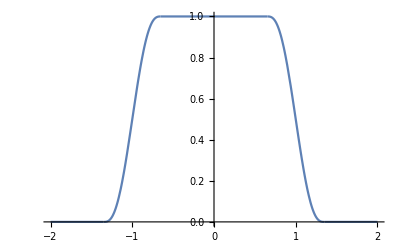

```mathematica
Plot[w[r],{r,-2,2}]
```